# Имитационная модель рабочего дня таксопарка

## Крестьянинов Александр ПМ-2101

## Цели и задачи

Цели

Реализовать алгоритм имитирующий работу таксопарка

Задачи

Парсинг и форматирование данных с сайта нью-йоркского такси

Создание настраиваемого алгоритма имитации

Визуализация данных

## О данных

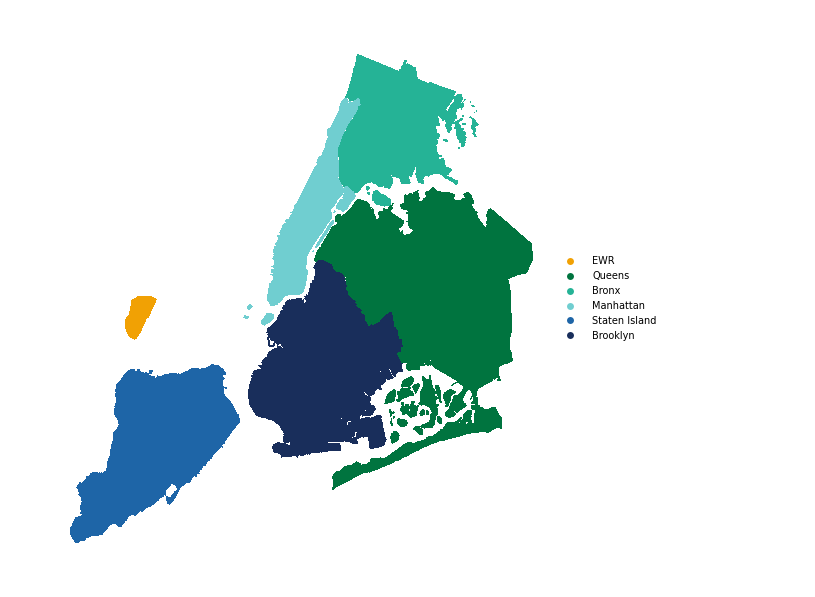

## Пример нумерации в Бронксе

## Информация о заказе

```mathematica
->
```

## Алгоритм

## Пример распределения машин в Манхэттене

## Определение “лучшей” машины

Время, нужное такси, чтобы доехать до заказчика

Готовность заказчика ожидать такси (константа waitingTime)

Запас топлива (оставшееся количество километров)

Время, чтобы доделать текущий заказ (при необходимости)

```mathematica
CarScope[order_List,car_List, hour_]:= With[
{index = Sequence[hour,car[[fz]],order[[szone]]]},
Module[
{dist = matrixSet[[1,index]],
time =  matrixSet[[2,index]], dopTime},
dopTime = PositiveRound[car[[ft]]-order[[stime]]]+time ;
{waitingTime-dopTime, {order[[fzone]],order[[ftime]]+dopTime ,car[[gas]]-dist-order[[distance]], car[[amount]]+order[[price]], car[[count]]+1}}
]
]
```

## Район в представлении PriorityQueue

```mathematica
queue =CreateDataStructure["PriorityQueue"];
queueEnteries = {{-1 * FinishedTime, CarId}};
queue["Push", #]&/@queueEnteries;
```

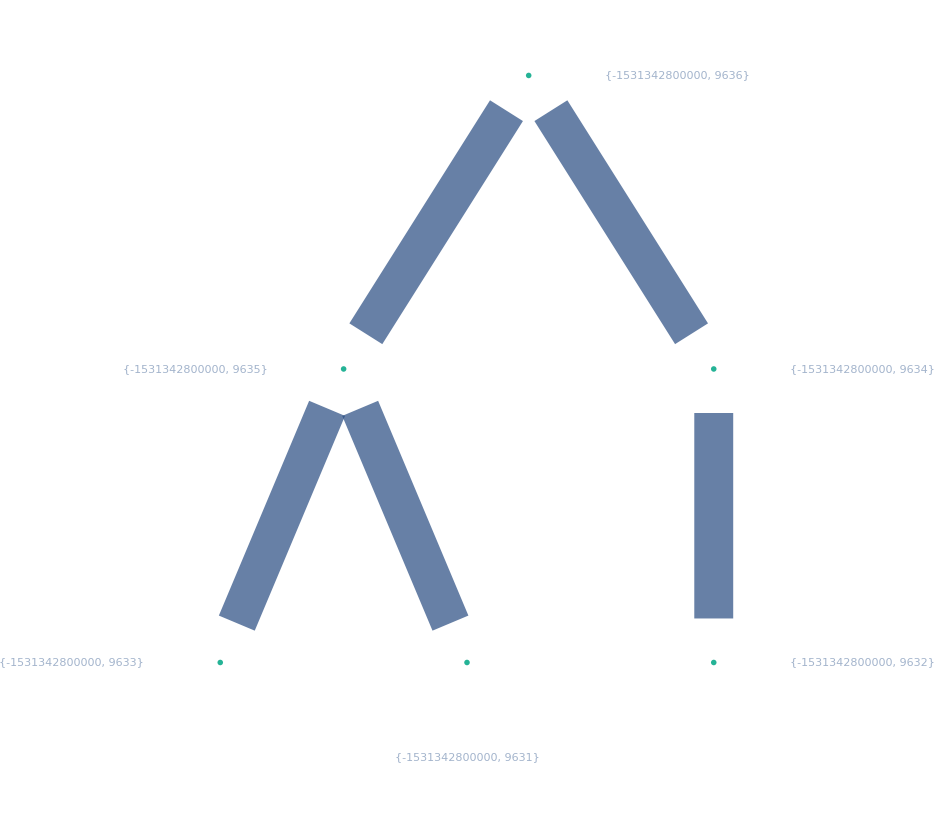
## 

## Немного о визуализации районов

```mathematica
123
```

## Анализ рабочего дня

```mathematica
-Graphics- + -Graphics-
```

=

```mathematica
GoOneDay[sortedOrders_, carsCount_]:=Module[{matrixSet, cars, nearestZones ,carsHab, lostClients = 0, CarScope, SelectCar},
CarScope[order_List,car_List, hour_]:= With[
{index = Sequence[hour,car[[fz]],order[[szone]]]},
Module[
{dist = matrixSet[[1,index]],
time =  matrixSet[[2,index]], dopTime},
dopTime = PositiveRound[car[[ft]]-order[[stime]]]+time ;
{waitingTime-dopTime, {order[[fzone]],order[[ftime]]+dopTime ,car[[gas]]-dist-order[[distance]], car[[amount]]+order[[price]], car[[count]]+1}}
]
];
SelectCar[order_]:=Module[{
hour = GetNumberHour[order]+1, scope, selectedCar},
selectedCar=Flatten@MinimalBy[Map[{#,cars[[#]]}&,Map[If[carsHab[[#]]["EmptyQ"],Nothing,carsHab[[#]]["Peek"][[2]]]&,nearestZones[[hour,order[[szone]]]]]],#[[2,ft]]&, UpTo[1]];
If[selectedCar != {},
scope=CarScope[order, selectedCar[[2;;]], hour];
Module[
{carId = selectedCar[[1]], 
dopTime = scope[[1]],
 newCar = scope[[2]]},
If[dopTime>=0,
carsHab[[cars[[carId,fz]]]]["Pop"];
carsHab[[newCar[[fz]]]]["Push", {-newCar[[ft]], carId}];
cars[[carId]]= FillCar@newCar;
carId,
lostClients++; -1
]
],
lostClients++; -1
]
];
matrixSet = GetMatrixSet[sortedOrders];
cars = GetCars[sortedOrders, carsCount];
nearestZones = GetNearestZones[matrixSet[[2]]];
carsHab = Table[CreateDataStructure["PriorityQueue"], 263];
MapIndexed[carsHab[[#[[fz]]]]["Push", {-#[[ft]],#2[[1]]}]&,cars];
{Sequence@@AbsoluteTiming[SelectCar/@ sortedOrders],PercentForm[(Length@sortedOrders-lostClients+0.)/Length@sortedOrders],
Total@cars[[All, amount]]}
]
```